```mathematica
fontName="Times";
SetOptions[Plot,FrameStyle->Directive[Thickness[0.002],13,fontName],GridLines->Automatic,GridLinesStyle->Directive[Thickness[0.001],Black],LabelStyle->(FontFamily->fontName),ImageSize->300,Frame->True,PlotStyle->Thick];
```

```mathematica
A={0,-d};L2={l Cos[θ[t]],l Sin[θ[t]]};L1=-L2;
Subscript[R, a]=L1-A;Subscript[R, b]=-A;Subscript[R, c]=L2-A;
Subscript[r, a]=(Subscript[R, a].Subscript[R, a])^(1/2);Subscript[r, b]=(Subscript[R, b].Subscript[R, b])^(1/2);Subscript[r, c]=(Subscript[R, c].Subscript[R, c])^(1/2);
```

```mathematica
Subscript[r, ba]=({{Cos[θ[t]], -Sin[θ[t]]}, {Sin[θ[t]], Cos[θ[t]]}}).({-l,0 });
Subscript[r, bb]={0,0};
Subscript[r, bc]=({{Cos[θ[t]], -Sin[θ[t]]}, {Sin[θ[t]], Cos[θ[t]]}}).({l,0 });
Cm=Subscript[k, c]({{1/R1, 1/Subscript[r, a], 1/Subscript[r, b], 1/Subscript[r, c]}, {1/Subscript[r, a], 1/R2a, 1/l, 1/2l}, {1/Subscript[r, b], 1/l, 1/R2b, 1/l}, {1/Subscript[r, c], 1/2l, 1/l, 1/R2c}});
Cm1=Inverse[Cm]//Simplify;
({{q10}, {q2a}, {q2b}, {q2c}})=Cm1.({{-Φ}, {Φ}, {Φ}, {Φ}});
```

```mathematica
Subscript[F, 2a]=-(Subscript[k, c] q10 q2a)/Subscript[r, a]^3 Subscript[R, a];
Subscript[F, 2b]=-(Subscript[k, c] q10 q2b)/Subscript[r, b]^3 Subscript[R, b];
Subscript[F, 2c]=-(Subscript[k, c] q10 q2c)/Subscript[r, c]^3 Subscript[R, c];
Qa[t_]:=-Subscript[k, c]q2a q10;
Qc[t_]:=-Subscript[k, c]q2c q10;
```

```mathematica
ET=(J θ'[t]^2)/2
```

1/2 J θ'[t]^2

```mathematica
1/2 J θ'[t]^2
```

1/2 J θ'[t]^2

ReplaceRepeated::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {{20000→20000,8.99×10^9→8.99×10^9,0.59→0.59,0.59→0.59,0.65→0.65,0.5→0.5,1.5→1.5,15→15,1000→1000}==-8.99×10^9 («1») ((8.89878×10^-6 (-0.896422+1.53846 Plus[«2»]+0.0888889 Power[«2»]))/(28.3926+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»])+(4.44939×10^-6 («5»+2 Plus[«2»]))/(28.3926+Times[«2»]+«4»+Times[«2»]+Times[«2»])-(«22» («20»+«4»))/(«19»+«6»+Times[«2»])+(4.44939×10^-6 (0.00666667-1.36752 Plus[«3»]))/(28.3926+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]))} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::naqs: «1» is not a quantified system of equations and inequalities.

Solve[-8.99×10^9 (-(0.0000241538/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]]))))))+(4.44939×10^-6 (0.0839925-5.21512/(√(227.25-45. Sin[θ[t]]))+2.30769/(√(227.25+45. Sin[θ[t]]))+0.444444 (2/(√(227.25-45. Sin[θ[t]]))-2/(√(227.25+45. Sin[θ[t]])))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))+(4.44939×10^-6 (0.0839925+2.30769/(√(227.25-45. Sin[θ[t]]))-5.21512/(√(227.25+45. Sin[θ[t]]))+0.444444 (-2/(√(227.25-45. Sin[θ[t]]))+2/(√(227.25+45. Sin[θ[t]])))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))+(2.22469×10^-6 (-0.616063-2/(√(227.25-45. Sin[θ[t]]))-2/(√(227.25+45. Sin[θ[t]]))+0.666667 (6.77966/(√(227.25-45. Sin[θ[t]]))+6.77966/(√(227.25+45. Sin[θ[t]])))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))) ((4.44939×10^-6 (-2.51977+0.225989/(√(227.25-45. Sin[θ[t]]))-0.1/(√(227.25+45. Sin[θ[t]]))-1.33333/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+2/(340.875+67.5 Sin[θ[t]])))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))+(8.89878×10^-6 (-0.896422+0.0888889/(√(227.25+45. Sin[θ[t]]))+1.53846 (3.38983-1/(227.25+45. Sin[θ[t]]))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))-(4.44939×10^-6 (0.0839925-5.21512/(√(227.25-45. Sin[θ[t]]))+2.30769/(√(227.25+45. Sin[θ[t]]))+0.444444 (2/(√(227.25-45. Sin[θ[t]]))-2/(√(227.25+45. Sin[θ[t]])))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))+(4.44939×10^-6 (0.00666667-1.36752 (2.075-2.25/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+0.065 (1/(√(227.25-45. Sin[θ[t]]))+1/(√(227.25+45. Sin[θ[t]]))))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]]))))))//.{20000→20000,8.99×10^9→8.99×10^9,0.59→0.59,0.59→0.59,0.65→0.65,0.5→0.5,1.5→1.5,15→15,1000→1000}==-8.99×10^9 (-(0.0000241538/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]]))))))+(4.44939×10^-6 (0.0839925-5.21512/(√(227.25-45. Sin[θ[t]]))+2.30769/(√(227.25+45. Sin[θ[t]]))+0.444444 (2/(√(227.25-45. Sin[θ[t]]))-2/(√(227.25+45. Sin[θ[t]])))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))+(4.44939×10^-6 (0.0839925+2.30769/(√(227.25-45. Sin[θ[t]]))-5.21512/(√(227.25+45. Sin[θ[t]]))+0.444444 (-2/(√(227.25-45. Sin[θ[t]]))+2/(√(227.25+45. Sin[θ[t]])))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))+(2.22469×10^-6 (-0.616063-2/(√(227.25-45. Sin[θ[t]]))-2/(√(227.25+45. Sin[θ[t]]))+0.666667 (6.77966/(√(227.25-45. Sin[θ[t]]))+6.77966/(√(227.25+45. Sin[θ[t]])))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))) ((8.89878×10^-6 (-0.896422+1.53846 (3.38983-1/(227.25-45. Sin[θ[t]]))+0.0888889/(√(227.25-45. Sin[θ[t]]))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))+(4.44939×10^-6 (-2.51977-0.1/(√(227.25-45. Sin[θ[t]]))-1.33333/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+2 (1/(340.875-67.5 Sin[θ[t]])+0.112994/(√(227.25+45. Sin[θ[t]])))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))-(4.44939×10^-6 (0.0839925+2.30769/(√(227.25-45. Sin[θ[t]]))-5.21512/(√(227.25+45. Sin[θ[t]]))+0.444444 (-2/(√(227.25-45. Sin[θ[t]]))+2/(√(227.25+45. Sin[θ[t]])))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))+(4.44939×10^-6 (0.00666667-1.36752 (2.075-2.25/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+0.065 (1/(√(227.25-45. Sin[θ[t]]))+1/(√(227.25+45. Sin[θ[t]]))))))/(28.3926-4/(15 √(227.25-45. Sin[θ[t]]))-4/(87.1504-17.2575 Sin[θ[t]])-4/(87.1504+17.2575 Sin[θ[t]])-4/(15 √(227.25+45. Sin[θ[t]]))+9.23077/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]]))+1.77778 (-6.77966+1/(227.25-45. Sin[θ[t]])+1/(227.25+45. Sin[θ[t]])-2/(√(227.25-45. Sin[θ[t]]) √(227.25+45. Sin[θ[t]])))+0.666667 (8.+8/15 (1.69492/(√(227.25-45. Sin[θ[t]]))+1.69492/(√(227.25+45. Sin[θ[t]])))))),θ[t]]

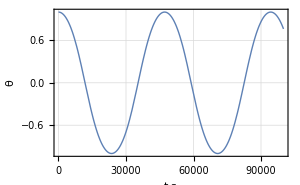

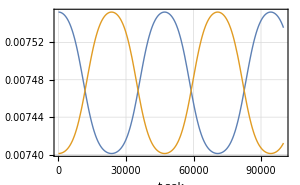

```mathematica
params={Φ->20000,Subscript[k, c]->8.99 10^9,R2a->.59,R2c->.59,R2b->.65,R1->.5,l->1.5,d->15,J->1000};
tk=100000;
eq = D[D[ET, D[θ[t],t]],t]-D[ET,θ[t]]==Q1//.params;
sol = NDSolve[{eq,θ[0]==1.,θ'[0]==0.},θ[t],{t,0,tk}];
cross =Qa[t]//.params==Qc[t]//.params;
Solve[cross,θ[t]]

Plot[{θ[t]}/.sol//Evaluate,{t,0,tk},AxesLabel->{"t,s","θ"},PlotRange->All]
Plot[{Qa[t]//.params,Qc[t]//.params}/.sol//Evaluate,{t,0,tk},AxesLabel->{"t,sek","θ"},PlotRange->All]
```

```mathematica
}
```